```mathematica
θ0 = Pi/4;
R = 100*h;
μ = 3/10;
μ = 0.3;
F=R*h;
βц=(3*(1-μ^2))^(1/4)/Sqrt[R*h]*Sqrt[h^2]/h;
βк=(3*(1-μ^2))^(1/4)/Sqrt[R/Sin[θ0]*h]*Sqrt[h^2]/h;
Dц=Emod*h^3/(12*(1-μ^2));
Dк=Emod*h^3/(12*(1-μ^2));
(*Податливости цилиндра*)
δ11ц = 1/(βц*Dц);
δ12ц = 1/(2*βц^2*Dц);
δ21ц = δ12ц;
δ22ц = 1/(2*βц^3*Dц);
(*Податливости конуса*)
δ11к = 1/(βк*Dк);
δ12к = Sin[θ0]/(2*βк^2*Dк);
δ21к = δ12к;
δ22к = Sin[θ0]^2/(2*βк^3*Dк);
```

```mathematica
(*Перемещения цилиндра*)
υц=δ11ц*m+δ12ц*x1
ρц= -δ21ц*m-δ22ц*x1+p*R^2/(Emod*h)*(1-μ/2)
```

(84.9536 m)/(Emod h^2)+(330.454 x1)/(Emod h)

-(330.454 m)/(Emod h)+(8500. h p)/Emod-(2570.81 x1)/Emod

```mathematica
(*Перемещения конуса*)
υк=δ11к*m+δ12к*(x2+1/2*p*R*Cot[θ0])-0*3/2*p/(Emod*h)*Cot[θ0]^2*R/Cos[θ0]//Simplify//Expand
(*υк=δ11к*m+δ12к*(x2+1/2*p*R*Cot[θ0])//N//Expand*)
ρк= -δ21к*m-δ22к*(x2+1/2*p*R*Cot[θ0])+p*R^2/(Emod*h*Sin[θ0])*(1-μ/2)//Expand
```

(101.027 m)/(Emod h^2)+(16522.7 p)/Emod+(330.454 x2)/(Emod h)

-(330.454 m)/(Emod h)-(96068.6 h p)/Emod-(2161.79 x2)/Emod

```mathematica
(*Перемещения шпангоута*)
δ22шп=R^2/(Emod*F)
ρшп=δ22шп*(x1+x2)
```

100/Emod

(100 (x1+x2))/Emod

```mathematica
(*Уравнения совместности*)
eq1=υк==-υц
eq2=ρк==ρшп
eq3=ρц==ρшп
Res= Solve[eq1&&eq2&&eq3,{m,x1,x2}]//First//Simplify;
Res//N
```

(101.027 m)/(Emod h^2)+(16522.7 p)/Emod+(330.454 x2)/(Emod h)==-(84.9536 m)/(Emod h^2)-(330.454 x1)/(Emod h)

-(330.454 m)/(Emod h)-(96068.6 h p)/Emod-(2161.79 x2)/Emod==(100 (x1+x2))/Emod

-(330.454 m)/(Emod h)+(8500. h p)/Emod-(2570.81 x1)/Emod==(100 (x1+x2))/Emod

{m→-39.853 h^2 p,x1→9.50153 h p,x2→-37.0721 h p}

```mathematica
(*Полученные перемещения*)
```

```mathematica
ρцRes=ρц/.Res;
ρцRes//N
ρкRes=ρц/.Res;
ρкRes//N
υцRes=υц/.Res;
υцRes//N
υкRes=υк/.Res;
υкRes//N
ρцбм=p*R^2/(Emod*h)*(1-μ/2);
ρкбм= p*R^2/(Emod*h*Sin[θ0])*(1-μ/2);
ρцкэ= -δ21ц*m-δ22ц*x1/.Res;
ρккэ= -δ21к*m-δ22к*(x2+1/2*p*R*Cot[θ0])/.Res;
```

-(2757.05 h p)/Emod

-(2757.05 h p)/Emod

-(245.841 p)/Emod

(245.841 p)/Emod

```mathematica
(*Силовые факторы*)
M1ц=m/.Res;
M1ц//N
M2ц=μ*M1ц;
M2ц//N
T1ц=1/2*p*R
T2ц=p*R

M1к=m/.Res;
M2к=μ*M1ц;
T1к=1/2*p*R*Sin[θ0]-x2*Cos[θ0]/.Res//N;
Q=1/2*p*R*Cos[θ0]+x2*Sin[θ0]/.Res//N;
T2к=p*R/Sin[θ0]//N;
```

-39.853 h^2 p

-11.9559 h^2 p

50 h p

100 h p

-(11257.1 h p)/Emod

-(2757.05 h p)/Emod

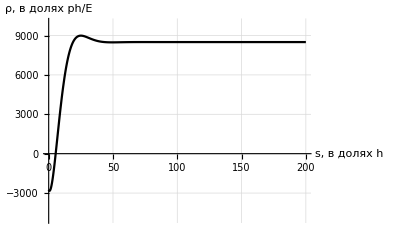

```mathematica
(*Итоговые графики перемещений*)
(*Цилиндр*)

ρцResFuncБМ[s_]=p*R^2/(Emod*h)*(1-μ/2)//N//Expand;
ρцResFuncКЭ1[s_]=-m/(Sqrt[2]*βц^2*Dц)*Exp[-βц*s]*Cos[βц*s+Pi/4]/.Res;
ρцResFuncКЭ2[s_]=-x1/(2*βц^3*Dц)*Exp[-βц*s]*Cos[βц*s]/.Res;
Simplify[ρцResFuncКЭ1[0]+ρцResFuncКЭ2[0],Assumptions->{h>0}]//Expand//N
ρцResFunc[s_]=ρцResFuncБМ[s]+ρцResFuncКЭ1[s]+ρцResFuncКЭ2[s];
Simplify[ρцResFunc[0],Assumptions->{h>0}]//Expand

example={h->1,Emod->1,p->1};
Plot[ρцResFunc[s]/.example,{s,0,2*R/.example},PlotRange->{-5000, 10000},GridLines->Automatic,AxesLabel->{"s, в долях h","ρ, в долях ph/E"},PlotStyle->{Black,Black}]
```

-(14777.9 h p)/Emod

-(2757.05 h p)/Emod

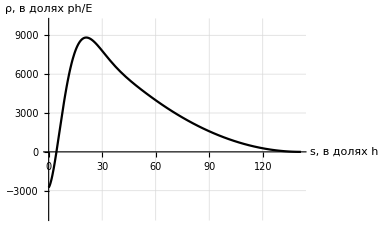

```mathematica
(*Конус*)

ρкResFuncБМ[s_]:=p*(R-s*Cos[θ0])^2/(Emod*h*Sin[θ0])*(1-μ/2)//N//Expand;
β[s_]:=Simplify[(3*(1-μ^2))^(1/4)/Sqrt[(R-s*Cos[θ0])/Sin[θ0]*h],h>0]
ρкResFuncКЭ1[s_]:=-m*Sin [θ0]/(Sqrt[2]*β[s]^2*Dк)*Exp[-β[s]*s]*Cos[β[s]*s+Pi/4]/.Res
ρкResFuncКЭ2[s_]:=-(x2+1/2*p*R*Cot[θ0])*Sin[θ0]^2/(2*β[s]^3*Dк)*Exp[-β[s]*s]*Cos[β[s]*s]/.Res
Simplify[ρкResFuncКЭ1[0]+ρкResFuncКЭ2[0],Assumptions->{h>0}]//Expand//N
ρкResFunc[s_]:=ρкResFuncБМ[s]+ρкResFuncКЭ1[s]+ρкResFuncКЭ2[s]
Simplify[ρкResFunc[0],Assumptions->{h>0}]//Expand//N

example={h->1,Emod->1,p->1};
Plot[ρкResFunc[s]/.example,{s,0,R/Cos[θ0]/.example},PlotRange->{-5000, 10000},GridLines->Automatic,AxesLabel->{"s, в долях h","ρ, в долях ph/E"},PlotStyle->{Black,Black}]
```

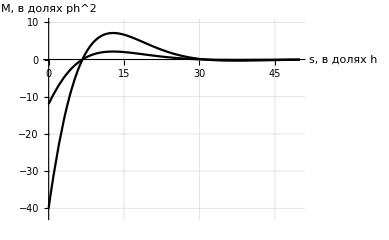

0.-39.853 h^2 p

0.-11.9559 h^2 p

```mathematica
(*Силовые факторы*)
(*Цилиндр*)
M1цResFunc[s_]=(-Dц*D[(ρцResFuncКЭ1[sv]+ρцResFuncКЭ2[sv]),{sv,2}])/.sv->s;
M2цResFunc[s_]:=μ*M1цResFunc[s];
Plot[{M1цResFunc[s]/.example,M2цResFunc[s]/.example},{s,0,0.5*R/.example},PlotRange->{-42,10},GridLines->Automatic,AxesLabel->{"s, в долях h","M, в долях ph^2"},PlotStyle->{Black,Black}]
Simplify[M1цResFunc[0],Assumptions->{h>0}]//Expand//N
Simplify[M2цResFunc[0],Assumptions->{h>0}]//Expand//N
```

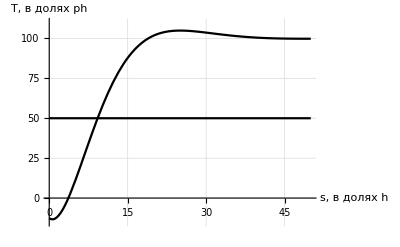

50 h p

-12.5705 h p

```mathematica
T1цResFunc[s_]:=T1ц;
T2цResFunc[s_]:=T2ц+Emod*h/R*(ρцResFuncКЭ1[s]+ρцResFuncКЭ2[s]);
Plot[{T1цResFunc[s]/.example,T2цResFunc[s]/.example},{s,0,0.5*R/.example},PlotRange->{-15,110},GridLines->Automatic,AxesLabel->{"s, в долях h","T, в долях ph"},PlotStyle->{Black,Black}]
T1цResFunc[0]
T2цResFunc[0]//N
```

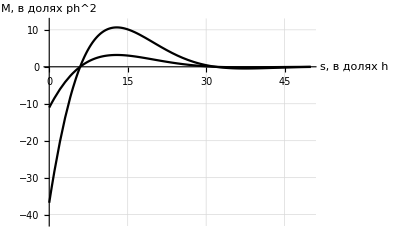

-36.7918 h^2 p

-11.0375 h^2 p

```mathematica
(*Конус*)
ρкResFuncКЭ1[s_]:=-m*Sin [θ0]/(Sqrt[2]*β[s]^2*Dк)*Exp[-β[s]*s]*Cos[β[s]*s+Pi/4]/.Res

ρкResFuncКЭ2[s_]:=-(x2+1/2*p*R*Cot[θ0])*Sin[θ0]^2/(2*β[s]^3*Dк)*Exp[-β[s]*s]*Cos[β[s]*s]/.Res
M1кResFunc[s_]=(-Dк/Sin[θ0]*D[(ρкResFuncКЭ1[sv]+ρкResFuncКЭ2[sv]),{sv,2}])/.sv->s;
M2кResFunc[s_]:=μ*M1кResFunc[s];
Plot[{M1кResFunc[s]/.example,M2кResFunc[s]/.example},{s,0,0.5*R/.example},PlotRange->{-42,12},GridLines->Automatic,AxesLabel->{"s, в долях h","M, в долях ph^2"},PlotStyle->{Black,Black}]
Simplify[M1кResFunc[0]//Expand,Assumptions->{h>0}]//N
Simplify[M2кResFunc[0]//Expand,Assumptions->{h>0}]//N
```

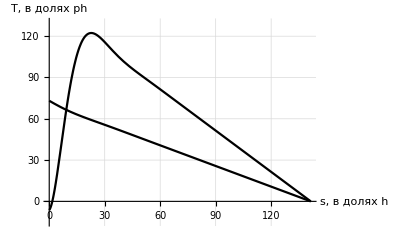

73.1034 h p

-6.35733 h p

```mathematica
T1кResFunc[s_]:=1/2*p*(R/Sin[θ0]-s)*Cot[θ0]-(Dк/Sin[θ0]^2*D[(ρкResFuncКЭ1[sv]+ρкResFuncКЭ2[sv]),{sv,3}]*CosIntegral[θ0])/.sv->s;
T2кResFunc[s_]:=p*(R-s*Cos[θ0])/Sin[θ0]+Emod*h/(R-s*Cos[θ0])*(ρкResFuncКЭ1[s]+ρкResFuncКЭ2[s]);
Plot[{T1кResFunc[s]/.example,T2кResFunc[s]/.example},{s,0,R/Cos[θ0]/.example},PlotRange->{-15,130},GridLines->Automatic,AxesLabel->{"s, в долях h","T, в долях ph"},PlotStyle->{Black,Black},PlotStyle->{Black,Black}]
Simplify[T1кResFunc[0]//Expand,Assumptions->{h>0}]//Expand//N
Simplify[T2кResFunc[0]//Expand,Assumptions->{h>0}]//Expand//N
```

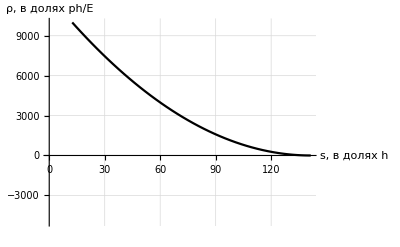

-0.155678 h^2 p

-0.155678 h^2 p

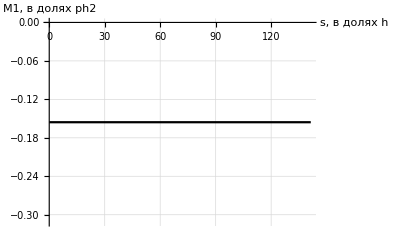

```mathematica
(*Вклад в моменты конуса от безмоментных перещемений*)
Plot[ρкResFuncБМ[s]/.example,{s,0,R/Cos[θ0]/.example},PlotRange->{-5000, 10000},GridLines->Automatic,AxesLabel->{"s, в долях h","ρ, в долях ph/E"},PlotStyle->{Black,Black}]
M1кResFuncБМ[s_]=(-Dк/Sin[θ0]*D[ρкResFuncБМ[sv],{sv,2}])/.sv->s
M1кResFuncБМ[0]
Plot[M1кResFuncБМ[s]/.example,{s,0,R/Cos[θ0]/.example},PlotRange->Automatic,GridLines->Automatic,AxesLabel->{"s, в долях h","M1, в долях ph2"},PlotStyle->{Black,Black}]
```

3/10

0.3

1.52862/(√(h (200. h-1.41421 s)))

-42.4602 h^2 p

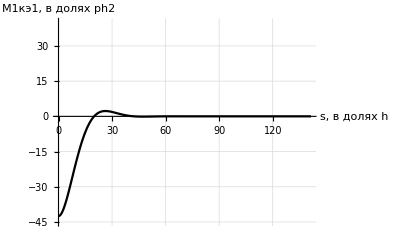

```mathematica
(*Вклад в моменты конуса от КЭ1*)

μ=3/10
μ=0.3
β[s]//N
ρкResFuncКЭ1[s_]:=-m*Sin [θ0]/(Sqrt[2]*β[s]^2*Dк)*Exp[-β[s]*s]*Cos[β[s]*s+Pi/4]/.Res
M1кResFuncКЭ1[s_]=(-Dк/Sin[θ0]*D[ρкResFuncКЭ1[sv],{sv,2}])/.sv->s;
Simplify[M1кResFuncКЭ1[0],Assumptions->{h>0}]//N
Plot[M1кResFuncКЭ1[s]/.example,{s,0,R/Cos[θ0]/.example},PlotRange->{-45,40},GridLines->Automatic,AxesLabel->{"s, в долях h","M1кэ1, в долях ph2"},PlotStyle->{Black,Black}]
```

5.66838 h^2 p

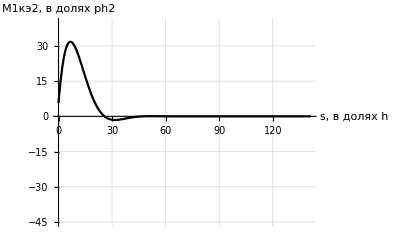

```mathematica
(*Вклад в моменты конуса от КЭ2*)

(*μ=0.3
μ=3/10
β[s]//N*)
ρкResFuncКЭ2[s_]=-(x2+1/2*p*R*Cot[θ0])*Sin[θ0]^2/(2*β[s]^3*Dк)*Exp[-β[s]*s]*Cos[β[s]*s]/.Res;
M1кResFuncКЭ2[s_]=(-Dк/Sin[θ0]*D[ρкResFuncКЭ2[sv],{sv,2}])/.sv->s;
Simplify[M1кResFuncКЭ2[0],Assumptions->{h>0}]//N
Plot[M1кResFuncКЭ2[s]/.example,{s,0,R/Cos[θ0]/.example},PlotRange->{-45,40},GridLines->Automatic,AxesLabel->{"s, в долях h","M1кэ2, в долях ph2"},PlotStyle->{Black,Black}]
```

-39.626 h^2 p

-11.8878 h^2 p

-36.7918 h^2 p

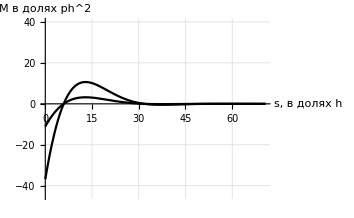

```mathematica
ρкКЭ1[s_]:=-m*Sin [θ0]/(Sqrt[2]*β[s]^2*Dк)*Exp[-β[s]*s]*Cos[β[s]*s+Pi/4]/.Res
M1кКЭ1[s_]=(-Dк/Sin[θ0]*D[ρкКЭ1[sv],{sv,2}])/.sv->s;


ρкКЭ2[s_]:=-(x2+1/2*p*R*Cot[θ0])*Sin[θ0]^2/(2*β[s]^3*Dк)*Exp[-β[s]*s]*Cos[β[s]*s]/.Res
M1кКЭ2[s_]=(-Dк/Sin[θ0]*D[ρкКЭ2[sv],{sv,2}])/.sv->s;


ρкКЭ[s_]=ρкКЭ1[s]+ρкКЭ2[s];
M1кКЭ[s_]=(-Dк/Sin[θ0]*D[ρкКЭ[sv],{sv,2}])/.sv->s;


Simplify[M1кКЭ1[0],Assumptions->{h>0}]+Simplify[M1кКЭ2[0],Assumptions->{h>0}]//Expand//N
μ*Simplify[M1кКЭ1[0],Assumptions->{h>0}]+μ*Simplify[M1кКЭ2[0],Assumptions->{h>0}]//Expand//N
Simplify[M1кКЭ[0],Assumptions->{h>0}]//Expand//N
Plot[{M1кКЭ1[s]+M1кКЭ2[s],μ*(M1кКЭ1[s]+M1кКЭ2[s])}/.example,{s,0,R/Cos[θ0]/2/.example},PlotRange->{-45,40},GridLines->Automatic,AxesLabel->{"s, в долях h","M в долях ph^2"},PlotStyle->{Black,Black}]
```

```mathematica
-39.62599201505874 h^2 p-0.15567765567765565 h^2 p
```

-39.7817 h^2 p